```mathematica
s[t_]:=1/π σ/(t^2+σ^2) Sin[ω t]
Ν=1000;
σ=2.4;
ω=1;
sn[T_]:=Table[{t,s[t]},{t,-T/2.+T/(2 Ν),T/2-T/(2 Ν),T/Ν}]
```

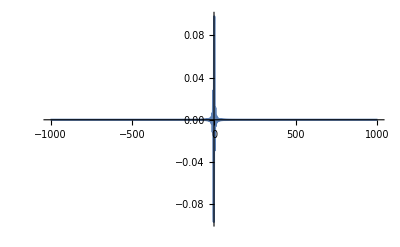

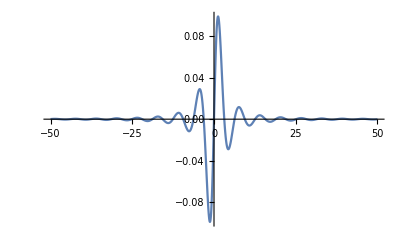

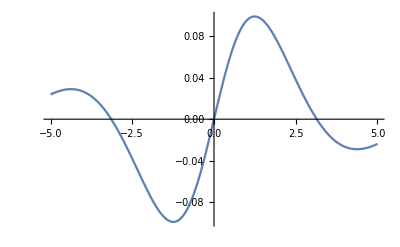

```mathematica
Plot[s[t],{t,-1000,1000},PlotRange->All]
Plot[s[t],{t,-50,50},PlotRange->All]
Plot[s[t],{t,-5,5},PlotRange->All]
```

```mathematica
fs[ν_]=FourierTransform[s[t],t,ν,FourierParameters->{0,-2 Pi}];
absfs[ν_]=Abs[fs[ν]]^2;
```

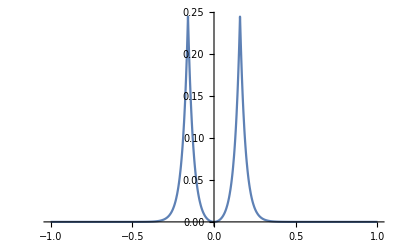

```mathematica
Plot[absfs[ν],{ν,-1,1},PlotRange->All]
```

```mathematica
fsn[T_]:=Table[{z/T,T/Ν Total[(#[[2]]&/@sn[T]) Array[ⅇ^(-ⅈ 2 π z #/Ν)&,Ν,{1.,Ν}]]},{z,-Ν/2.+1,Ν/2}]
absfsn[T_]:={#[[1]],Abs[#[[2]]]^2}&/@fsn[T]
```

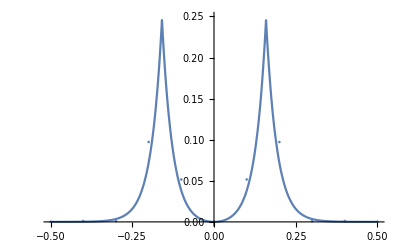

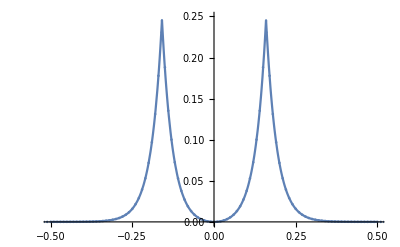

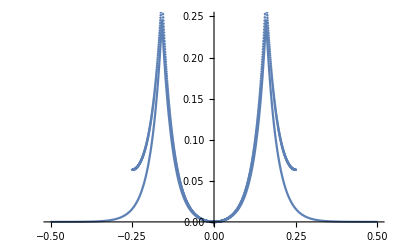

```mathematica
Show[Plot[absfs[ν],{ν,-.5,.5},PlotRange->{0,.25}],ListPlot[absfsn[10]],PlotRange->{{-.5,.5},{0,.25}}]
Show[Plot[absfs[ν],{ν,-.5,.5},PlotRange->{0,.25}],ListPlot[absfsn[100]],PlotRange->{{-.5,.5},{0,.25}}]
Show[Plot[absfs[ν],{ν,-.5,.5},PlotRange->{0,.25}],ListPlot[absfsn[2000]],PlotRange->{{-.5,.5},{0,.25}}]
```

```mathematica
Ν=10;
Timing[fsn[100]][[1]]
Timing[Fourier[(#[[2]]&/@sn[100]),FourierParameters->{1,-1}]][[1]]
Ν=100;
Timing[fsn[100]][[1]]
Timing[Fourier[(#[[2]]&/@sn[100]),FourierParameters->{1,-1}]][[1]]
Ν=1000;
Timing[fsn[100]][[1]]
Timing[Fourier[(#[[2]]&/@sn[100]),FourierParameters->{1,-1}]][[1]]
```

0.015625

0.

0.40625

0.

40.0781

0.046875

```mathematica
Clear["Global`*"]
```

```mathematica
V[x_]:=-Sech[x]^2
F[x_]=-D[V[x],x];
tmax=1000;
```

```mathematica
y[t_]=x[t]/.NDSolve[{x''[t]==F[x[t]],x[0]==-2,x'[0]==0},x[t],{t,0,tmax}][[1]]
```

InterpolatingFunction[{{0., 1000.}}, <>][t]

```mathematica
Ν=500;
xn=Table[{t,y[t]},{t,tmax/(2 Ν),tmax-tmax/(2 Ν),tmax/Ν}];
fxn=Table[{z/tmax,tmax/Ν Total[(#[[2]]&/@xn) Array[ⅇ^(-ⅈ 2 π z #/Ν)&,Ν,{1.,Ν}]]},{z,-Ν/2.+1,Ν/2}];
absfxn={#[[1]],Abs[#[[2]]]^2}&/@fxn;
```

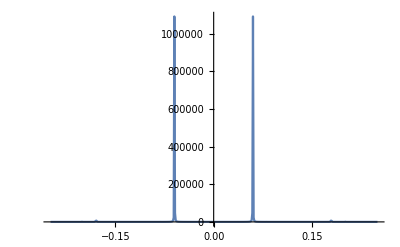

```mathematica
ListLinePlot[absfxn,PlotRange->All]
```

```mathematica
2 Pi #[[1]]&/@MaximalBy[absfxn,Last]
```

{-0.376991,0.376991}

```mathematica
2 Pi/(√2 NIntegrate[1/(√(V[-2]-V[x])),{x,-2,2}])
```

0.375901

```mathematica
y[t_,Ω_]:=x[t]/.NDSolve[{x''[t]==F[x[t]]+Sin[Ω t]-.1 x'[t],x[0]==-2,x'[0]==0},x[t],{t,0,tmax}][[1]]
```

```mathematica
yn[Ω_]:=Block[{yi=y[t,Ω]},Table[{t,yi},{t,tmax/(2 Ν),tmax-tmax/(2 Ν),tmax/Ν}]]
fyn[Ω_]:=Table[{z/tmax,tmax/Ν Total[(#[[2]]&/@yn[Ω]) Array[ⅇ^(-ⅈ 2 π z #/Ν)&,Ν,{1.,Ν}]]},{z,-Ν/2.+1,Ν/2}]
absfyn[Ω_]:={#[[1]],Abs[#[[2]]]^2}&/@fyn[Ω]
```